# MATH7501 Practical 7 (Week 8), Semester 1-2021

## Topic: Sequences, Limits and Series

Author:  Aminath Shausan
Date: 23-04-2021

# Pre-Tutorial Activity

Students must have familiarised themselves with unit 5 contents  of the reading materials for MATH7501

# Resources

Chapter 5 and 6 of course reader

# Q1 Limit of sum of two sequences

Suppose lim_(n⟶∞) a_n = a and lim_(n⟶∞) b_n = b. 
Use the(ε,N)definition of the limit of a sequence to show that 
                            lim_(n⟶∞) (a_n + b_n) = a +b

Solution: 
Since lim_(n⟶∞) a_n = a, there exists an N_1 such that, for every ϵ_1>0, if n ≥ N_1 then |a_n-a| < ϵ_1. Similarly, as lim_(n⟶∞) b_n = b, there exists an N_2 such that, for every ϵ_2>0, if n ≥ N_2 then |b_n-b| < ϵ_2.

Now, choose ϵ>0 such that ϵ ≥ϵ_1+ϵ_2 and and integer N such that N = max(N_1,N_2). Then we have 
|(a_n+b_n)-(a+b)| ≤ |a_n-a|+|b_n-b|, by the triangle inequality
                                             < ϵ_1+ϵ_2
                                               ≤ ϵ
This implis that lim_(n⟶∞) (a_n + b_n) = a +b.

The last inequality holds for any ϵ_1 and ϵ_2 such that ϵ_1+ϵ_2 ≤ϵ. Thus leting ϵ_1= ϵ_2=ϵ/2 would satisfy this condition. In the above proof, we choose N = max(N_1,N_2)to avoid the case that  if N_1<N_2, then for all n ≥ N_1 we have |a_n-a| < ϵ_1.  However, if n<N_2, we have |b_n-b| > ϵ_2.

# Q2 Derivative of sin(x)

(a) Give a geometric explanation of why d/dx sin(x) = cos(x)

Solution :
 Note that by definition, derivative of a function at a given point is given by the slope of the tangent line at that point. Below is the graph of sin (x) and cos (x) on the same plot for x in the range [-3, 3].  Consider the sin (x) curve, and imagine drawing tangent lines at points on the curve. For example, if x = 0,  the slope of the tangent line  on sin (x) curve is 1, which coincides with cos (0) = 1. At the two turning points, on sin (x), the slope of the tangent line is 0, which coincides with cos (x) = 0. Repeating this process, it looks like that the derivative of sin (x) is cos (x). 
  
  The above explanation is only a visualisation of the proof, but not a formal proof.  A formal proof is explained using a unit circle and right - triangle identities for sin (x) and cos (x). You may refer to this link (which is an MIT OpenCourseWare handout) for a detailed explanation of such a proof.

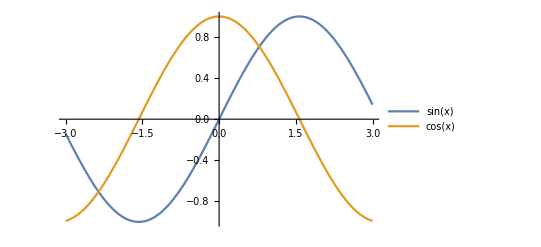

```mathematica
Plot[{Sin[x],Cos[x]},{x, -3,3}, PlotLegends-> "Expressions"]
```

(b) prove the result in part (a) using using the fact that 
           T:  = sin (x + h) = sin (x) cos (h) + cos (x) sin (h), 
           l_1:=  sin (h)/h tends to 1 as h tends to 0 
           l_(2: =)cos (h) - 1)/h tends to 0 as h tends to 0.

Solution:
Using the definition of the derivative, we have that 
d/dx sin(x) = limit_(h → 0)(sin(x+h) - sin(x))/h
                       = limit_(h → 0)(sin(x)cos(h)+cos(x )sin(h)- sin(x))/h , by T
                        = limit_(h → 0)(cos(x)sin(h)- sin(x)+sin(x)cos(h))/h
                        = limit_(h → 0)(cos(x)sin(h)+ sin(x)[cos(h)-1])/h
                         = cos(x)[limit_(h → 0)(sin(h))/h] +sin(x) [limit_(h → 0)(cos(h)-1)/h]
                        = cos(x)×1 + sin(x)×0 ,   by l_1 and l_2
                        = cos(x)

Below are visual plot to show l_1 and l_2. The  first plot shows that 
                        limit_(x → 0)(sin(x))/x=1 
and the second plot shows that 
                     limit_(x → 0)(cos(x)-1)/x=0

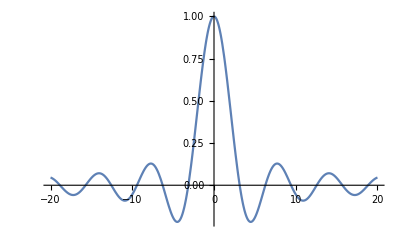

```mathematica
Plot[Sin[x]/x,{x, -20,20}, PlotRange->All]
```

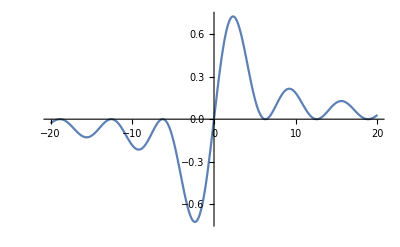

```mathematica
Plot[(1-Cos[x])/x,{x, -20,20}, PlotRange->All]
```

# Q3 Product rule, chain rule and quotient rule

(a) Using only the product rule and the fact that dx/dx=1,calculate d/dx(x^3)

Solution:
d/dx(x^3) =d/dx(xx^2), writing x^3 = x x^2
                 = d/dx(x)x^2+ x d/dx(x^2), by the product rule
                 = 1  x^2 +x [d/dx(x x)] , writing x^2 = x x
                 = x^2 +x [d/dx(x )x + x d/dx(x ) ] , by the product rule 
                 = x^2 +x [1 x + 1 x ]
                  = x^2 +2 x^2
                 = 3 x^2

(b) Prove the quotient rule for derivatives using the chain rule, the product rule and the power rule

Solution:
Let h(x)  = (f(x))/(g(x)). Then   h(x)  = f((x)[ g(x)])^-1. 
 d/dxh(x) = d/dx(f((x)[ g(x)])^-1) 
                             = d/dx((f(x))[ g(x)])^-1+ f(x) d/dx([ g(x)]^-1), by the product rule
                             = d/dx((f(x))[ g(x)])^-1+ f(x) {-(1[ g(x)])^-2d/dx[ g(x)]}, by the power rule and chain rule
                             = (d/dx(f(x)))/[ g(x)]- (f(x) d/dx[ g(x)])/[ g(x)]^2
                               = (d/dx(f(x))g(x) - f(x) d/dx[ g(x)])/[ g(x)]^2

# Q4 Evaluation of a series and approximations

Consider S =∑_(n=1)^∞ n^-2 , for n =1, 2,3...
(a) Use Mathematica to analytically evaluate S.

```mathematica
Sum[1/n^2, {n, 1, Infinity}]
```

π^2/6

(b) Use this result to suggest an algorithm for numerically approximating the constant π and implement it in Mathematica.

Solution:
From part (a), we have S = π^2/6.  Rearanging this for π gives π = √(6S). Using this formular, we can  obtain a numerical approximation for π as:   limit_(k → ∞)√[6 ∑_(n=1)^k n^-2]. The following program computes this approximation and plots the approximated value for each k value.

```mathematica
Clear[f]
```

```mathematica
(* first create a function to compute the value of √[6 ∑_(n=1)^k n^-2] for each k and check if its output is close to the numerical value of π = 3.141592653589793*)
f[k_]:=Sqrt[6Sum[1/n^2,{n, 1, k}]]
```

```mathematica
N[f[100]]
```

3.13208

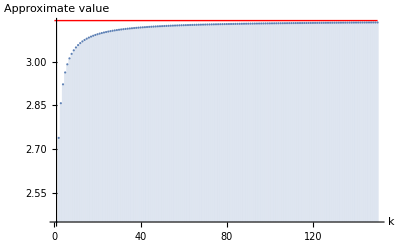

```mathematica
(* write a program to compute the approximation for k in [1 to nmax]. You can choose the value for nmax *)
With[{nmax = 150},                                                             (*nmax is the upper limit of the sum*)
   Show[ DiscretePlot[f[k], {k, 1, nmax}, 
Epilog->{Red,Line[{{0,Pi},{nmax,Pi}}]},   (*This plots a hrizontal red line showing the actual value of π*)
PlotRange->All,
AxesLabel-> {k, Approximate value}
]]
]
```

As seen from the plot, the approximation is getting close to the actual value of π as k  increases. If you wish to know which k value gives an absolute difference between the approximated value and the actual value for a given tolerance value (error), the following code may be used. Note that in this example, I chose the error to be 0.0001 in this example.

```mathematica
Clear[k]
FindRoot[Abs[f[k]-Pi]==0.0001,{k,1000}]
```

{k→9548.95}

# Q5 Harmonic series

Consider the harmonic series S =∑_(n=1)^∞ n^-1 , for n =1, 2,3.... The partial sum of S is given by 
 ∑_(n=1)^k n^-1 = log(k) + γ + ϵ_k, 
where γ is Euler’s gamma constant and ϵ_k is an o(1) sequence. Use Mathematica to numerically approximate γ.

```mathematica
Solution:
As Subscript[ϵ, k] is an o(1) sequence, it converges to zero in probability as k approaches to an appropriate limit. Then γ can be approximated by 
                                γ = Subscript[limit, k -> ∞] [∑_(n=1)^k n^-1 - log(k)]. The approximated value, up to fifteen decimal places, is γ=0.577215664901532(see here). We can compute this constant numerically by following a similar algorithm as we constructed for Q4.
```

```mathematica
Clear[g]
(* first create a function to compute the value of [∑_(n=1)^k n^-1 - log(k)] for each k and check if its output is close to the numerical value of γ= 0.57721 56649 01532*)
g[k_]:=Sum[1/n,{n, 1, k}]- Log[k]
```

```mathematica
N[g[1000]]
```

0.577716

```mathematica
(* write a program to compute the approximation for k in [1 to nmax]. You can choose the value for nmax *)
```

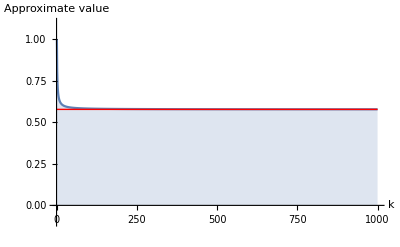

```mathematica
With[{nmax=1000},
DiscretePlot[g[k],{k,1,nmax},
Epilog->{Red,Line[{{0,0.5772},{nmax,0.5772}}]},
PlotRange->{{0,nmax},{-.1, 1.1}},
AxesLabel-> {k, Approximate value}
]]
```

```mathematica
It is seen from the plot that the approximate value converges to the actual value (the red line) of γ as k approaches infinity.
```

# Q6 Optimisation

suppose f(x) = 1/(1+x^2). Use derivatives to explain why x=0 is the only maximum

First derivative test can be used to show this. The derivative of f(x) with respect to x is given by 
f'(x) =(-2x)/(1+ x^2). 
Solving f'(x)=0 gives x =0 as the only critical point. 
Now, if x<0, then f'(x) >0, imlying that f(x) is increasing for x<0.
If x> 0, then f'(x) <0, imlying that f(x) is decreasing for x<0. Thus, there is a local maximum at x=0 and since it is the only critical  point, it must be  a global maximum.

# Q7 Limit

Find the limit of x/(√(1+x^2)) as x tends to infinity

```mathematica
Subscript[limit, x-> ∞](x/(√(1+x^2))) = Subscript[limit, x-> ∞](x/(√(x^2(1+1/x^2)))) , factrise x^2
                                               = Subscript[limit, x-> ∞](x/(x √(1+1/x^2))) , √x^2 = x
                     = Subscript[limit, x-> ∞](1/(√(1+1/x^2))) ,  
                                                 = 1/(√(1+ 0)),  Subscript[limit, x-> ∞](1/x^2) = 0 , 
                                                 = 1
```